## Eqns

```mathematica
Sov[Ω0_,q_]:=Module[{a1,a2},
a1=Solve[ x^2(1+2(Ω0/x)^(1/3))(1+2(Ω0/x)^(1/3)+2(Ω0/x)^(2/3))==(1+(Ω0/x)^(1/3))^2 q^2,x,Assumptions->{x>0,x+Ω0^(1/3)x^(2/3)>=0}][[1,1,2]];
a2=Ω0^(2/3)a1^(4/3)/(Ω0^(1/3)a1^(2/3)+a1)-Ω0^(1/3)a1^(2/3);
a1+I*a2];
```

```mathematica
x=Ω0;
Solve[ x^2(1+2(Ω0/x)^(1/3))(1+2(Ω0/x)^(1/3)+2(Ω0/x)^(2/3))==(1+(Ω0/x)^(1/3))^2 q^2,q]
Clear[x];
```

{{q→-(√15 Ω0)/2},{q→(√15 Ω0)/2}}

```mathematica
ex=FullSimplify[(1+2(xbyom)^(-1/3))(1+2(xbyom)^(-1/3)+2(xbyom)^(-2/3))-(1+(xbyom)^(-1/3))^2 qbyom^2 xbyom^-2/.xbyom->1/z^3,Assumptions->z∈ Reals && z>0]
```

1+4 z+6 z^2+4 z^3-qbyom^2 z^6 (1+z)^2

```mathematica
ser=Series[ex,{z,∞,0}]
eq=Normal[ser]
Simplify[Solve[4 z^3-qbyom^2 z^6 (z)^2==0,z],Assumptions->{q,z}∈ Reals && z>0 && q>0]
```

-qbyom^2 z^8-2 qbyom^2 z^7-qbyom^2 z^6+4 z^3+6 z^2+4 z+1+O[1/z]^1

1+4 z+6 z^2+4 z^3-qbyom^2 z^6-2 qbyom^2 z^7-qbyom^2 z^8

{{z→0},{z→0},{z→0},{z→(-2)^(2/5)/qbyom^(2/5)},{z→2^(2/5)/qbyom^(2/5)},{z→-((-1)^(1/5) 2^(2/5))/qbyom^(2/5)},{z→-((-1)^(3/5) 2^(2/5))/qbyom^(2/5)},{z→((-1)^(4/5) 2^(2/5))/qbyom^(2/5)}}

```mathematica
(-1)^(1/5)//N
```

0.809017+0.587785 ⅈ

```mathematica
1/(2^(2/5*3)/qbyom^(2/5*3))
```

qbyom^(6/5)/(2 2^(1/5))

```mathematica
ser=Series[ex,{z,0,6}]
eq=Normal[ser]
Solve[1==qbyom^2 z^6,z]
```

1+4 z+6 z^2+4 z^3-qbyom^2 z^6+O[z]^7

1+4 z+6 z^2+4 z^3-qbyom^2 z^6

{{z→-1/qbyom^(1/3)},{z→1/qbyom^(1/3)},{z→-(-1)^(1/3)/qbyom^(1/3)},{z→(-1)^(1/3)/qbyom^(1/3)},{z→-(-1)^(2/3)/qbyom^(1/3)},{z→(-1)^(2/3)/qbyom^(1/3)}}

```mathematica
1.0/9
6.0/5
```

0.111111

1.2

```mathematica
Solve[xbyom==1/z^3,xbyom]
```

{{xbyom→1/z^3}}

```mathematica
ser=Series[(xbyom^2(1+2(xbyom)^(-1/3))(1+2(xbyom)^(-1/3)+2(xbyom)^(-2/3))-(1+(xbyom)^(-1/3))^2 qbyom^2)(xbyom)^(2/3),{xbyom,0,2}]
eq=Normal[ser]
Solve[qbyom^2==4 xbyom^(5/3),xbyom]
Ω0^(1-6/5) 1/(2 2^(1/5))/.Ω0->0.01//N
```

-qbyom^2-2 qbyom^2 xbyom^(1/3)-qbyom^2 xbyom^(2/3)+4 xbyom^(5/3)+6 xbyom^2+O[xbyom]^(7/3)

-qbyom^2-2 qbyom^2 xbyom^(1/3)-qbyom^2 xbyom^(2/3)+4 xbyom^(5/3)+6 xbyom^2

{{xbyom→((qbyom^2)^(3/5))/(2 2^(1/5))}}

1.09336

```mathematica
FullSimplify[Ω0^(2/3)a1^(4/3)/(Ω0^(1/3)a1^(2/3)+a1)-Ω0^(1/3)a1^(2/3)/.a1->2^(-6/5) q^(6/5)Ω0^(-1/5),Assumptions->{q,a}∈ Reals && z>0 && q>0]
FullSimplify[Series[%,{q,0,2}]]//Normal
%/.Ω0->0.01//N
```

-(q^(6/5) Ω0^(1/5))/(2^(4/5) q^(2/5)+2 2^(1/5) Ω0^(2/5))

-q^2/(4 Ω0)+q^(8/5)/(2 2^(3/5) Ω0^(3/5))-q^(6/5)/(2 2^(1/5) Ω0^(1/5))

-1.09336 q^(6/5)+5.2282 q^(8/5)-25. q^2

```mathematica
Series[Ω0^(2/3)a1^(4/3)/(Ω0^(1/3)a1^(2/3)+a1)-Ω0^(1/3)a1^(2/3),{a1,0,2}]
```

-a1+a1^(4/3)/Ω0^(1/3)-a1^(5/3)/Ω0^(2/3)+a1^2/Ω0+O[a1]^(7/3)

```mathematica
ser=Series[xbyom^2(1+2(xbyom)^(-1/3))(1+2(xbyom)^(-1/3)+2(xbyom)^(-2/3))-(1+(xbyom)^(-1/3))^2 qbyom^2,{xbyom,∞,1}]
eq=Normal[ser]
Solve[qbyom^2==xbyom^2,xbyom]
```

xbyom^2+4 xbyom^(5/3)+6 xbyom^(4/3)+4 xbyom-qbyom^2-2 qbyom^2 (1/xbyom)^(1/3)-qbyom^2 (1/xbyom)^(2/3)+O[1/xbyom]^(4/3)

-qbyom^2-qbyom^2/xbyom^(2/3)-(2 qbyom^2)/xbyom^(1/3)+4 xbyom+6 xbyom^(4/3)+4 xbyom^(5/3)+xbyom^2

{{xbyom→-qbyom},{xbyom→qbyom}}

```mathematica
im=FullSimplify[Ω0^(2/3)a1^(4/3)/(Ω0^(1/3)a1^(2/3)+a1)-Ω0^(1/3)a1^(2/3)/.a1-> q,Assumptions->{q,z}∈ Reals && z>0 && q>0]
FullSimplify[Series[im,{q,0,2}]]
Normal[%]/.Ω0->0.01//N
(* below is the correct scale *)
FullSimplify[Series[im,{Ω0,0,2}]]
Normal[%]/.Ω0->0.01//N
```

-(q Ω0^(1/3))/(q^(1/3)+Ω0^(1/3))

-q+q^(4/3)/Ω0^(1/3)-q^(5/3)/Ω0^(2/3)+q^2/Ω0-q^(7/3)/Ω0^(4/3)+q^(8/3)/Ω0^(5/3)+O[q]^3

-1. q+4.64159 q^(4/3)-21.5443 q^(5/3)+100. q^2-464.159 q^(7/3)+2154.43 q^(8/3)

-q^(2/3) Ω0^(1/3)+q^(1/3) Ω0^(2/3)-Ω0+Ω0^(4/3)/q^(1/3)-Ω0^(5/3)/q^(2/3)+Ω0^2/q+O[Ω0]^(7/3)

-0.01+0.0001/q-0.000464159/q^(2/3)+0.00215443/q^(1/3)+0.0464159 q^(1/3)-0.215443 q^(2/3)

## Below Ω0

```mathematica
Om0=0.01;
dat1=Table[{q,Sov[Om0,q]},{q,10^-5,(√15 Om0)/10,(√15 Om0)/2/1000}]//Quiet;
list=dat1;
len=Length[list];
dat1=Table[{list[[i,1]],Re[list[[i,2]]]},{i,1,len}];
dat2=Table[{list[[i,1]],-Im[list[[i,2]]]},{i,1,len}];
datr1=Table[{list[[i,1]],-Im[list[[i,2]]]/Re[list[[i,2]]]},{i,1,len}];
th=0.01;
style={Directive[Darker[Blue],Thickness[0.01]],Directive[Orange,Thickness[0.01]],Directive[Darker[Cyan],Thickness[0.01],Dashing[0.01]],Directive[Darker[Green],Thickness[0.01],Dashing[0.01]]};
(* 2^(-6/5) q^(6/5) Ω0^(-1/5); coeff.~1.0933620739432781 *)
FindFit[Drop[dat1,0],a  q^b,{a,b},q]
fnre[q_]=a  q^b/. %;
datfitr=Table[{q,(*2^(-6/5) q^(6/5) Om0^(-1/5)*)fnre[q]},{q,10^-5,(√15 Om0)/10,(√15 Om0)/2/1000}];
(***** imag part ******** -1.0933620739432781 q^(6/5)+5.228197762956365 q^(8/5) **)
FindFit[dat2,a  q^(6/5)-b q^(8/5),{a,b,c,d},q]
fnim[q_]=a  q^(6/5)-b q^(8/5)/. %;
datfiti=Table[{q,(*q^(6/5)/(2^(6/5) Om0^(1/5))-q^(8/5)/(2^(8/5) Om0^(3/5))*)fnim[q]},{q,10^-5,(√15 Om0)/10,(√15 Om0)/2/1000}];
```

{a→1.19588,b→1.20495}

{a→1.04673,b→2.65229,c→0.,d→0.}

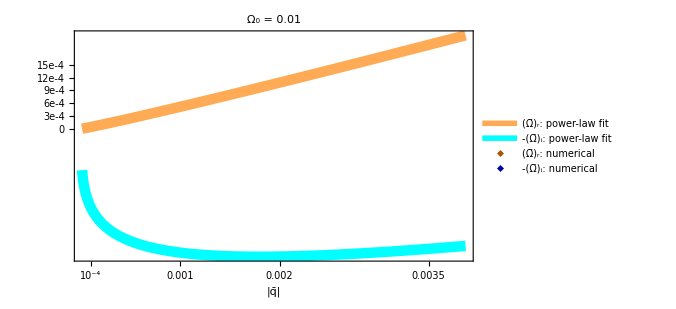

```mathematica
np=ListPlot[{dat1, dat2},Axes->None,Frame-> True,BaseStyle->{FontSize->20,Bold},FrameTicksStyle->Directive[Darker[Gray],18],FrameTicks->{{{{0,"0"},{3*10^-4,"3e-4"},{6*10^-4,"6e-4"},{9*10^-4,"9e-4"},{12*10^-4,"12e-4"},{15*10^-4,"15e-4"}},None},{{{10^-4,"10^-4"},.001, .002,.0035},None}},FrameLabel->{Style["|q̄|",FontFamily->"TexMaths Roman",Black, Bold, 24],None},PlotStyle->{Darker[Orange],Darker[Blue]},PlotMarkers->{◆,Scaled[0.001]},
PlotLabel->Style["Ω_0 = 0.01",20,Brown,Bold],
PlotLegends->Placed[LineLegend[{"(Ω̄)_r: numerical","-(Ω̄)_i: numerical","(Ω̄)_r: power-law fit", "-(Ω̄)_i: power-law fit"},LabelStyle->{FontFamily->"TexMaths Roman",18},LegendLayout->"Column"],{Scaled[{0.5,1}],{1.3,0.99}}],ImageSize->500];

ap=Plot[{fnre[q],fnim[q]},{q,10^-5,(√15 Om0)/10},Axes->None,Frame-> True,BaseStyle->{FontSize->20,Bold},FrameTicksStyle->Directive[Darker[Gray],18],FrameTicks->{{{{0,"0"},{3*10^-4,"3e-4"},{6*10^-4,"6e-4"},{9*10^-4,"9e-4"},{12*10^-4,"12e-4"},{15*10^-4,"15e-4"}},None},{{{10^-4,"10^-4"},.001, .002,.0035},None}},FrameLabel->{Style["|q̄|",FontFamily->"TexMaths Roman",Black, Bold, 22],None},PlotStyle->{Directive[Lighter[Orange],Thickness[0.015]],Directive[Cyan,Thickness[0.015]]},
PlotLabel->Style["Ω_0 = 0.01",20,Brown,Bold],
PlotLegends->Placed[LineLegend[{"(Ω̄)_r: power-law fit", "-(Ω̄)_i: power-law fit"},LabelStyle->{FontFamily->"TexMaths Roman",18},LegendLayout->"Column"],{Scaled[{0.5,1}],{1.05,2}}],ImageSize->500];

p1=Show[ap,np]
(*SetDirectory[NotebookDirectory[]];Export["disp1.pdf",Rasterize[p1],ImageResolution->100];*)
```

```mathematica
low=(√15 Om0)/10
hi=(√15 Om0)/2
del=0.005;
dat11=Sort[Join[dat1,Table[{q,Sov[Om0,q]},{q,low+del,hi,del}]]//Quiet];
list=dat11;
len=Length[list];
dat1=Table[{list[[i,1]],Re[list[[i,2]]]},{i,1,len}];
dat2=Table[{list[[i,1]],-Im[list[[i,2]]]},{i,1,len}];
dat3=Table[{q,fnre[q]},{q,10^-5,hi,del}];
dat4=Table[{q,fnim[q]},{q,10^-5,hi,del}];
ListPlot[{dat1,dat2}, Joined->True,Axes->None,Frame-> True,BaseStyle->{FontFamily->"TexMaths Roman",FontSize->20,Bold},FrameTicksStyle->Directive[Darker[Gray],18],FrameTicks->{{Automatic,None},{Automatic,None}},PlotStyle->style]
```

0.00387298

0.0193649

```mathematica
dat11
```

## above Ω0

```mathematica
Om0=0.01;
dat1=Table[{q,Sov[Om0,q]},{q,(√15 Om0)/2 10,(√15 Om0)/2*100,del=(√15 Om0)/5}]//Quiet;
list=dat1;
len=Length[list];
dat1=Table[{list[[i,1]],Re[list[[i,2]]]},{i,1,len}];
dat2=Table[{list[[i,1]],-Im[list[[i,2]]]},{i,1,len}];
datr2=Table[{list[[i,1]],-Im[list[[i,2]]]/Re[list[[i,2]]]},{i,1,len}];
th=0.01;
style={Directive[Darker[Blue],Thickness[0.01]],Directive[Orange,Thickness[0.01]],Directive[Darker[Cyan],Thickness[0.01],Dashing[0.01]],Directive[Darker[Green],Thickness[0.01],Dashing[0.01]]};
(*  q *)
FindFit[dat1,a q^b,{a,b},q]
fnre[q_]=a  q^b/. %;
datfitr=Table[{q,a q^b/. %},{q,(√15 Om0)/2 10,(√15 Om0)/2*100,del}];

(** imag. part ->-q^(2/3) Ω0^(1/3)+q^(1/3) Ω0^(2/3)-Ω0 or -0.2154434690031884 q^(2/3) + 0.046415888336127795 q^(1/3) ****)
FindFit[dat2,a q^(2/3)+b q^(1/3),{a,b},q]
fnim[q_]=a q^(2/3)+b q^(1/3)/. %;
datfiti=Table[{q,(*q^(2/3) Om0^(1/3)-q^(1/3) Om0^(2/3)*)a q^(2/3)+b q^(1/3)/. %},{q,(√15 Om0)/2 10,(√15 Om0)/2*100,del}];
```

{a→0.81149,b→1.06516}

ReplaceAll::reps: {0.141202} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0.147226} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0.153265} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{a→0.201974,b→-0.0491533}

ReplaceAll::reps: {0.0391667} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0.0405834} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0.0419869} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

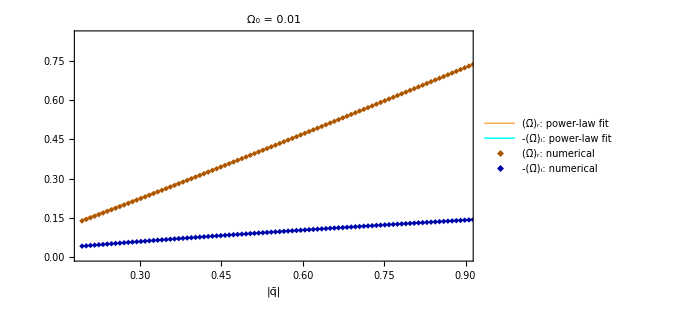

```mathematica
np=ListPlot[{dat1, dat2},Axes->None,Frame-> True,BaseStyle->{FontFamily->"TexMaths Roman",FontSize->20,Bold},FrameTicksStyle->Directive[Darker[Gray],18],FrameLabel->{Style["|q̄|",FontFamily->"TexMaths Roman",Black, Bold, 22],None},PlotStyle->{Darker[Orange],Darker[Blue]},PlotMarkers->{◆,Scaled[0.007]},
PlotLabel->Style["Ω_0 = 0.01",20,Brown,Bold],
PlotLegends->Placed[LineLegend[{"(Ω̄)_r: numerical","-(Ω̄)_i: numerical","(Ω̄)_r: power-law fit", "-(Ω̄)_i: power-law fit"},LabelStyle->{FontFamily->"TexMaths Roman",18},LegendLayout->"Column"],{Scaled[{0.5,1}],{1.35,0.99}}],ImageSize->500];

th=0.003;ap=Plot[{fnre[q],fnim[q]},{q,(√15 Om0)/2 10,(√15 Om0)/2*100},Axes->None,Frame-> True,PlotRange->{{(√15 Om0)/2 10,0.9},{0,0.85}},BaseStyle->{FontSize->20,Bold},FrameTicksStyle->Directive[Darker[Gray],16],FrameLabel->{Style["|q̄|",FontFamily->"TexMaths Roman",Black, Bold, 22],None},PlotStyle->{Directive[Lighter[Orange],Thickness[th]],Directive[Cyan,Thickness[th]]},
PlotLabel->Style["Ω_0 = 0.01",20,Brown,Bold],
PlotLegends->Placed[LineLegend[{"(Ω̄)_r: power-law fit", "-(Ω̄)_i: power-law fit"},LabelStyle->{FontFamily->"TexMaths Roman",18},LegendLayout->"Column"],{Scaled[{0.5,1}],{1.1,2}}],ImageSize->500];

p1=Show[ap,np]
(*SetDirectory[NotebookDirectory[]];Export["disp2.pdf",Rasterize[p1],ImageResolution->100];*)
```

### ratio plot

```mathematica
dat=Table[{q,Sov[Om0,q]},{q,(√15 Om0)/10,(√15 Om0)/2 10,(√15 Om0)/2/20}]//Quiet;
list=dat;
len=Length[list];
datr12=Table[{list[[i,1]],-Im[list[[i,2]]]/Re[list[[i,2]]]},{i,1,len}];
```

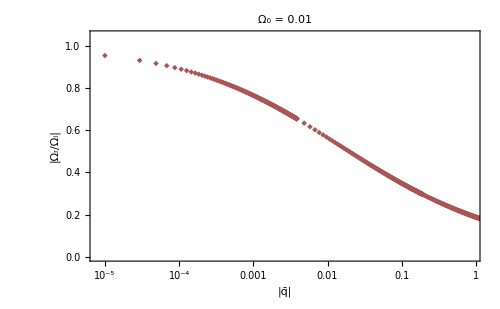

```mathematica
pl=ListLogLinearPlot[Join[datr1,datr12,datr2],Axes->None,Frame-> True,PlotRange->{{10^-5.1,0.9},{0,1.05}},LabelStyle->{FontSize->20,Bold,Black},FrameTicksStyle->Directive[Darker[Gray],16],FrameTicks->{{Automatic,None},{{{10^-5, "10^-5"},{10^-4,"10^-4"},{10^-3,"10^-3"},0.01,0.1, 0.8},None}},PlotStyle->Darker[Pink],FrameLabel->{Style["|q̄|", 22,FontFamily->"TexMaths Roman"],Style["|Ω_r/Ω_i|",FontFamily->"TexMaths Roman", 22]},PlotMarkers->{◆,Scaled[Small]},PlotLabel->Style["Ω_0 = 0.01",20,Brown,Bold],ImageSize->500]
(*SetDirectory[NotebookDirectory[]];Export["ratio.pdf",Rasterize[pl],ImageResolution->100];*)
```

### Other Ω0 value

{a→0.942811,b→1.06515}

-0.001+0.01 q^(1/3)-0.1 q^(2/3)

{a→0.0937354,c→-0.0105825}

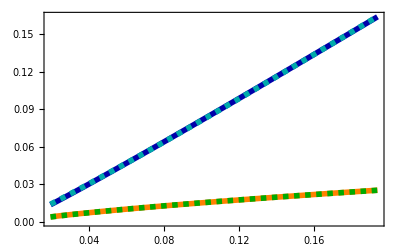

```mathematica
Om0=0.001;
dat1=Table[{q,Sov[Om0,q]},{q,(√15 Om0)/2 10,(√15 Om0)/2*100,del=(√15 Om0)/2}]//Quiet;
list=dat1;
len=Length[list];
dat1=Table[{list[[i,1]],Re[list[[i,2]]]},{i,1,len}];
dat2=Table[{list[[i,1]],-Im[list[[i,2]]]},{i,1,len}];
th=0.01;
style={Directive[Darker[Blue],Thickness[0.01]],Directive[Orange,Thickness[0.01]],Directive[Darker[Cyan],Thickness[0.01],Dashing[0.01]],Directive[Darker[Green],Thickness[0.01],Dashing[0.01]]};
(* 2^(-6/5) q^(6/5) Ω0^(-1/5); coeff.~1.0933620739432781 *)
FindFit[dat1,a q^b,{a,b},q]
datfitr=Table[{q,a q^b/. %},{q,(√15 Om0)/2 10,(√15 Om0)/2*100,del}];

(** imag. part ->-q^(2/3) Ω0^(1/3)+q^(1/3) Ω0^(2/3)-Ω0  ****)
-q^(2/3) Ω0^(1/3)+q^(1/3) Ω0^(2/3)-Ω0/.Ω0->Om0
FindFit[dat2,a q^(2/3)+c q^(1/3),{a,c},q]
datfiti=Table[{q,a q^(2/3)+c q^(1/3)/. %},{q,(√15 Om0)/2 10,(√15 Om0)/2*100,del}];
ListPlot[{dat1, dat2,datfitr,datfiti}, Joined->True,Axes->None,Frame-> True,PlotRange->{{(√15 Om0)/2 10,All},Automatic},BaseStyle->{FontFamily->"TexMaths Roman",FontSize->20,Bold},FrameTicksStyle->Directive[Darker[Gray],18],FrameTicks->{{Automatic,None},{Automatic,None}},PlotStyle->style]
```